# THE SC construction for the unit triangle 0, 1, ⅈ from the pre-vertices -1, 0, and 1

I need to find an f that matches. 
	f'(z)=C (z+1)^(-3/4)(z^(-1/2)(z-1))^(-3/4).
We need f to be analytic in the upper half plane.  A symbolic integration does not necessarily respect these branch cuts. I changed the pre-vertex labels to get a representation avoiding the #$#@ Appel function.  No reason for you to know this but the Hypergeometric function is much less esoteric!  The branch cuts match and the

```mathematica
fPrime[0.0]=0.0;
fPrime[z_]:=z^(-1/2)/((z+1)^(3/4)(z-1)^(3/4))
Integrate[fPrime[z],z]
f1[z_]:=(8 z (1-z^2)^(3/4) Hypergeometric2F1[5/16,3/4,21/16,z^2])/(5 ((-1+z) √z)^(3/4) (1+z)^(3/4))
TabView[{
"f'"->ComplexPlot3D[fPrime[z],{z,2}],
"f1"->ComplexPlot3D[f[z],{z,2}],
"check"->Plot3D[ Norm[f1'[x+ I y]-fPrime[x + I y]],{x, -3,3},{y,0,4}]
}]
```

(2 √z (1-z^2)^(3/4) Hypergeometric2F1[1/4,3/4,5/4,z^2])/((-1+z)^(3/4) (1+z)^(3/4))

123

```mathematica
Clear[f1,f2,F1,F2]
f1[z_]:=1/((z-1)^(3/4)(z+1)^(3/4));
f2[z_]:=1/((z^2-1)^(3/4));
F1[z_]=Integrate[f1[z],z]
F2[z_]=Integrate[f2[z],z]
TabView[{
"f1"->ComplexPlot3D[f1[z],{z,2}],
"f2"->ComplexPlot3D[f2[z],{z,2}],
"F1"->ComplexPlot3D[F1[z],{z,2}],
"F2"->ComplexPlot3D[F2[z],{z,2}]}]
```

2 2^(1/4) (-1+z)^(1/4) Hypergeometric2F1[1/4,3/4,5/4,(1-z)/2]

(z (1-z^2)^(3/4) Hypergeometric2F1[1/2,3/4,3/2,z^2])/((-1+z^2)^(3/4))

1234

```mathematica
MR=100;
ListPlot[
Flatten[Table[
ReIm[F1[x+ I y]],
{x,-MR,MR,0.1},
{y, ϵ, MI, 0.1}],1],
PlotRange->All
]
```

-Graphics-

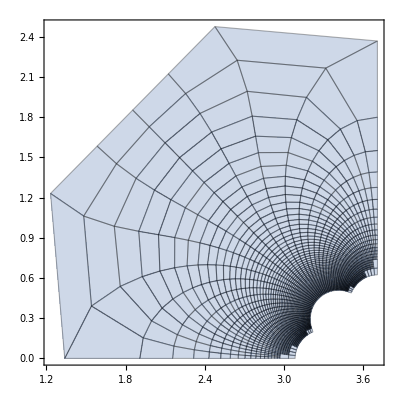

```mathematica
MR=10.3; MI=10; ϵ=0.0001;
ParametricPlot[ReIm[F1[x+I y]],{x, -MR,MR},{y,ϵ, MI},
PlotRange->All,Mesh->All]
```

I am choosing a small ϵ>0 to make sure we stay in the upper half plane!  These are the corners of our output triangle!

```mathematica
ϵ=10.0^-50;
{f1[0 + ϵ ⅈ],f1[1+ϵ ⅈ],f1[-1+ϵ ⅈ]}
```

{-8.82458×10^-32-1.75532×10^-32 ⅈ,-2.32239-2.32239 ⅈ,-1.25687-3.03435 ⅈ}

So we have fixed 0->0.  We still need to choose the scaling and rotation C  so that 
	f(z)=C f1(z) 
satisfies f(1)=C (-2.32239-2.32239 ⅈ)=ⅈ.  We need 
	C=ⅈ/(-2.32239-2.32239 ⅈ)=-0.215296-0.215296 ⅈ

```mathematica
I/(-2.3223872236868894-2.3223872236872976 ⅈ)
```

-0.215296-0.215296 ⅈ

```mathematica
f[z_]:=(-0.21529570732232522-0.2152957073222874 ⅈ)f1[z]
Chop[{f[0 + ϵ ⅈ],f[1+ϵ ⅈ],f[-1+ϵ ⅈ]}]
```

{0,0.+1. ⅈ,-0.382683+0.92388 ⅈ}

```mathematica
I/((-1.6245842300114113-1.624584230011819 ⅈ))
```

-0.307771-0.307771 ⅈ

```mathematica
ϵ=10.0^-50;
{f1[0 + ϵ ⅈ],f1[1+ϵ ⅈ],f1[-1+ϵ ⅈ]}
```

{1.26844×10^-69-2.52309×10^-70 ⅈ,-1.62458-1.62458 ⅈ,-0.879219+2.12262 ⅈ}

```mathematica
f[1+ϵ ⅈ]
```

-1.40485-1.53357 ⅈ

```mathematica
R=10^10;ϵ=0.0001;
f[R+ϵ ⅈ]
f[-R+ϵ ⅈ]
Graphics[ {EdgeForm[Red],
{LightGreen,Polygon[ {ReIm[0],ReIm[1],ReIm[ⅈ]}]},
{Cyan,Polygon[
{ ReIm[f[ϵ+ϵ ⅈ]],
ReIm[f[1+ϵ ⅈ]],ReIm[f[-1+ϵ ⅈ]],
ReIm[f[-R + ϵ I]],
ReIm[f[0+R ⅈ]]}]}
}, Frame->True]
```

```mathematica
R=10^23;ϵ=0.000001;
{f[ϵ+R ⅈ],
f[-R+ϵ ⅈ],
f[R+ϵ ⅈ]}
```

{8.16734-1.62458 ⅈ,8.15748-1.6205 ⅈ,8.15667-1.62458 ⅈ}

```mathematica
f[
```

```mathematica
f[10^12+0.001 I]
f[-10^12+0.001 I]
```

7.91435-1.62458 ⅈ

7.93361-1.52777 ⅈ

```mathematica
ParametricPlot[ ReIm[f[x+ I y]],{x, -10^8,10^8},{y,0,10^10},PlotRange->All,Mesh->Automatic,AspectRatio->Automatic]
```

-Graphics-

```mathematica
TabView[{
"Close-Up Origin"->ComplexPlot3D[fPrime[z],{z,2}],
"Upper-Half Plane"->ComplexPlot3D[fPrime[z],{z, -5+0.2 I ,5+3 I},PlotRange->{0,1.5},MaxRecursion->8]
}]
```

```mathematica
12
```

We can avoid the @#@# function by just integrating the derivative f' directly.  

Since F(z)=∫_0^z f'(ζ)dζ is independent of path in the upper half plane if we have a regularly spaced grid of value of the derivative f' then we can use horizontal aka real trapezoid steps
	f(x+Δx + ⅈ y)≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ Δx + ⅈ y))/2 Δx
and vertical aka imaginary trapezoid steps
	f(x + ⅈ (y+Δy))≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ ⅈ (y+Δy)))/2 ⅈ Δy
to step to any grid point starting from f(0)=0.  The branch cuts along the real axis suggest we first step up vertically from the origin to build a table of values along the positive imaginary axis. We can then step of the imaginary axis (in the positive and negative directions) to fill in the values of f on horizontal lines.   For the numerically inclined it is indeed true that it would be better to think about this in the centered form 
	f(x+Δx/2 + ⅈ y)≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ Δx + ⅈ y))/2 Δx
	f(x + ⅈ (y+Δy/2))≈f(x+ⅈ y)+(f'(x+ⅈ y) + f'(x+ ⅈ (y+Δy)))/2 ⅈ Δy.

I want this to look good at the end!  In this context this means that:

I need lots of values near the real axis y = 0 which is the boundary of the triangle!

I need lots of values near the singularities aka pre-vertices x=-1,0,1 which are the corners of the triangle.

I need to get well out the real axis to fill in the last edge of the triangle.

I need to get well out the positive imaginary axis to fill in the middle of the triangle.

To do this with a reasonable number of points we need a grid with different sized gaps.

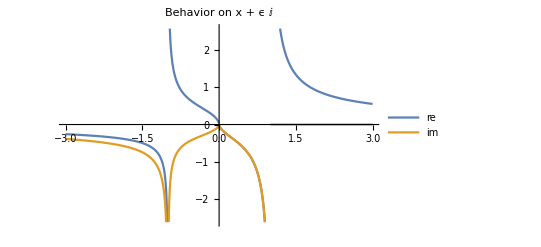

```mathematica
ϵ=10^-12;
Plot[{Re[fPrime[x + ϵ ⅈ]],Im[fPrime[x]]},{x,-3,3},
PlotLegends->{"re","im"},
PlotLabel->"Behavior on x + ϵ ⅈ"]
```